# N0=1 (*Air*) N1=1.4607 (*SiO_2*) N2=4.1360+ⅈ 0.010205 (*c-Si*)

```mathematica
1
```

1.4607

4.136+0.010205 ⅈ

```mathematica
r01p[θ_]=(N1 Cos[θ]-N0 Sqrt[1-(N0/N1 Sin[θ])^2])/(N1 Cos[θ]+N0 Sqrt[1-(N0/N1 Sin[θ])^2])
r12p[θ_]=(N2 Cos[θ]-N1 Sqrt[1-(N1/N2 Sin[θ])^2])/(N2 Cos[θ]+N1 Sqrt[1-(N1/N2 Sin[θ])^2])
r01s[θ_]=(N0 Cos[θ]-N1 Sqrt[1-(N0/N1 Sin[θ])^2])/(N1 Cos[θ]+N0 Sqrt[1-(N0/N1 Sin[θ])^2])
r12s[θ_]=(N1 Cos[θ]-N2 Sqrt[1-(N1/N2 Sin[θ])^2])/(N1 Cos[θ]+N2 Sqrt[1-(N1/N2 Sin[θ])^2])
```

(N1 cos(θ)-N0 √(1-(N0^2 sin^2(θ))/N1^2))/(N0 √(1-(N0^2 sin^2(θ))/N1^2)+N1 cos(θ))

(N2 cos(θ)-N1 √(1-(N1^2 sin^2(θ))/N2^2))/(N1 √(1-(N1^2 sin^2(θ))/N2^2)+N2 cos(θ))

(N0 cos(θ)-N1 √(1-(N0^2 sin^2(θ))/N1^2))/(N0 √(1-(N0^2 sin^2(θ))/N1^2)+N1 cos(θ))

(N1 cos(θ)-N2 √(1-(N1^2 sin^2(θ))/N2^2))/(N2 √(1-(N1^2 sin^2(θ))/N2^2)+N1 cos(θ))

```mathematica
β[θ]=(2π)/λ d Sqrt[N1^2-N0^2 Sin[θ]]
```

(2 π d √(N1^2-N0^2 sin(θ)))/λ

```mathematica
r3PHp[θ_]=(r01p[θ]+r12p[θ] Exp[ⅈ 2β[θ]])/(1+r01p[θ]r12p[θ]Exp[ⅈ 2 β[θ]])
r3PHs[θ_]=(r01s[θ]+r12s[θ] Exp[ⅈ 2β[θ]])/(1+r01s[θ]r12s[θ]Exp[ⅈ 2 β[θ]])
```

((N1 cos(θ)-N0 √(1-(N0^2 sin^2(θ))/N1^2))/(N0 √(1-(N0^2 sin^2(θ))/N1^2)+N1 cos(θ))+((N2 cos(θ)-N1 √(1-(N1^2 sin^2(θ))/N2^2)) ⅇ^((4 ⅈ π d √(N1^2-N0^2 sin(θ)))/λ))/(N1 √(1-(N1^2 sin^2(θ))/N2^2)+N2 cos(θ)))/(1+((N1 cos(θ)-N0 √(1-(N0^2 sin^2(θ))/N1^2)) (N2 cos(θ)-N1 √(1-(N1^2 sin^2(θ))/N2^2)) ⅇ^((4 ⅈ π d √(N1^2-N0^2 sin(θ)))/λ))/((N0 √(1-(N0^2 sin^2(θ))/N1^2)+N1 cos(θ)) (N1 √(1-(N1^2 sin^2(θ))/N2^2)+N2 cos(θ))))

((N0 cos(θ)-N1 √(1-(N0^2 sin^2(θ))/N1^2))/(N0 √(1-(N0^2 sin^2(θ))/N1^2)+N1 cos(θ))+((N1 cos(θ)-N2 √(1-(N1^2 sin^2(θ))/N2^2)) ⅇ^((4 ⅈ π d √(N1^2-N0^2 sin(θ)))/λ))/(N2 √(1-(N1^2 sin^2(θ))/N2^2)+N1 cos(θ)))/(1+((N0 cos(θ)-N1 √(1-(N0^2 sin^2(θ))/N1^2)) (N1 cos(θ)-N2 √(1-(N1^2 sin^2(θ))/N2^2)) ⅇ^((4 ⅈ π d √(N1^2-N0^2 sin(θ)))/λ))/((N0 √(1-(N0^2 sin^2(θ))/N1^2)+N1 cos(θ)) (N2 √(1-(N1^2 sin^2(θ))/N2^2)+N1 cos(θ))))

```mathematica
Rp[θ_]=r3PHp[θ]Conjugate[r3PHp[θ]]
Rs[θ_]=r3PHs[θ]Conjugate[r3PHs[θ]]
```

(((N1 cos(θ)-N0 √(1-(N0^2 sin^2(θ))/N1^2))/(N0 √(1-(N0^2 sin^2(θ))/N1^2)+N1 cos(θ))+((N2 cos(θ)-N1 √(1-(N1^2 sin^2(θ))/N2^2)) ⅇ^((4 ⅈ π d √(N1^2-N0^2 sin(θ)))/λ))/(N1 √(1-(N1^2 sin^2(θ))/N2^2)+N2 cos(θ))) Conjugate[((N1 cos(θ)-N0 √(1-(N0^2 sin^2(θ))/N1^2))/(√(1-(N0^2 sin^2(θ))/N1^2) N0+N1 cos(θ))+(ⅇ^((4 ⅈ d π √(N1^2-N0^2 sin(θ)))/λ) (N2 cos(θ)-N1 √(1-(N1^2 sin^2(θ))/N2^2)))/(√(1-(N1^2 sin^2(θ))/N2^2) N1+N2 cos(θ)))])/((1+((N1 cos(θ)-N0 √(1-(N0^2 sin^2(θ))/N1^2)) (N2 cos(θ)-N1 √(1-(N1^2 sin^2(θ))/N2^2)) ⅇ^((4 ⅈ π d √(N1^2-N0^2 sin(θ)))/λ))/((N0 √(1-(N0^2 sin^2(θ))/N1^2)+N1 cos(θ)) (N1 √(1-(N1^2 sin^2(θ))/N2^2)+N2 cos(θ)))) (1+(Conjugate[((N1 cos(θ)-N0 √(1-(N0^2 sin^2(θ))/N1^2)) (N2 cos(θ)-N1 √(1-(N1^2 sin^2(θ))/N2^2)))] exp(-(4 ⅈ π Conjugate[(d √(N1^2-N0^2 sin(θ)))])/Conjugate[λ]))/(Conjugate[(√(1-(N0^2 sin^2(θ))/N1^2) N0+N1 cos(θ))] Conjugate[(√(1-(N1^2 sin^2(θ))/N2^2) N1+N2 cos(θ))])))

(((N0 cos(θ)-N1 √(1-(N0^2 sin^2(θ))/N1^2))/(N0 √(1-(N0^2 sin^2(θ))/N1^2)+N1 cos(θ))+((N1 cos(θ)-N2 √(1-(N1^2 sin^2(θ))/N2^2)) ⅇ^((4 ⅈ π d √(N1^2-N0^2 sin(θ)))/λ))/(N2 √(1-(N1^2 sin^2(θ))/N2^2)+N1 cos(θ))) Conjugate[((N0 cos(θ)-N1 √(1-(N0^2 sin^2(θ))/N1^2))/(√(1-(N0^2 sin^2(θ))/N1^2) N0+N1 cos(θ))+(ⅇ^((4 ⅈ d π √(N1^2-N0^2 sin(θ)))/λ) (N1 cos(θ)-N2 √(1-(N1^2 sin^2(θ))/N2^2)))/(√(1-(N1^2 sin^2(θ))/N2^2) N2+N1 cos(θ)))])/((1+((N0 cos(θ)-N1 √(1-(N0^2 sin^2(θ))/N1^2)) (N1 cos(θ)-N2 √(1-(N1^2 sin^2(θ))/N2^2)) ⅇ^((4 ⅈ π d √(N1^2-N0^2 sin(θ)))/λ))/((N0 √(1-(N0^2 sin^2(θ))/N1^2)+N1 cos(θ)) (N2 √(1-(N1^2 sin^2(θ))/N2^2)+N1 cos(θ)))) (1+(Conjugate[((N0 cos(θ)-N1 √(1-(N0^2 sin^2(θ))/N1^2)) (N1 cos(θ)-N2 √(1-(N1^2 sin^2(θ))/N2^2)))] exp(-(4 ⅈ π Conjugate[(d √(N1^2-N0^2 sin(θ)))])/Conjugate[λ]))/(Conjugate[(√(1-(N0^2 sin^2(θ))/N1^2) N0+N1 cos(θ))] Conjugate[(√(1-(N1^2 sin^2(θ))/N2^2) N2+N1 cos(θ))])))

```mathematica
D[Rs[θ], θ]
```

(((N0 cos(θ)-N1 √(1-(N0^2 sin^2(θ))/N1^2))/(√(1-(N0^2 sin^2(θ))/N1^2) N0+N1 cos(θ))+(ⅇ^((4 ⅈ d π √(N1^2-N0^2 sin(θ)))/λ) (N1 cos(θ)-N2 √(1-(N1^2 sin^2(θ))/N2^2)))/(√(1-(N1^2 sin^2(θ))/N2^2) N2+N1 cos(θ))) Conjugate'((N0 cos(θ)-N1 √(1-(N0^2 sin^2(θ))/N1^2))/(√(1-(N0^2 sin^2(θ))/N1^2) N0+N1 cos(θ))+(ⅇ^((4 ⅈ d π √(N1^2-N0^2 sin(θ)))/λ) (N1 cos(θ)-N2 √(1-(N1^2 sin^2(θ))/N2^2)))/(√(1-(N1^2 sin^2(θ))/N2^2) N2+N1 cos(θ))) (-(2 ⅈ d ⅇ^((4 ⅈ d π √(N1^2-N0^2 sin(θ)))/λ) π cos(θ) (N1 cos(θ)-N2 √(1-(N1^2 sin^2(θ))/N2^2)) N0^2)/(λ √(N1^2-N0^2 sin(θ)) (√(1-(N1^2 sin^2(θ))/N2^2) N2+N1 cos(θ)))-((-(cos(θ) sin(θ) N0^3)/(N1^2 √(1-(N0^2 sin^2(θ))/N1^2))-N1 sin(θ)) (N0 cos(θ)-N1 √(1-(N0^2 sin^2(θ))/N1^2)))/((√(1-(N0^2 sin^2(θ))/N1^2) N0+N1 cos(θ))^2)+((N0^2 cos(θ) sin(θ))/(N1 √(1-(N0^2 sin^2(θ))/N1^2))-N0 sin(θ))/(√(1-(N0^2 sin^2(θ))/N1^2) N0+N1 cos(θ))+(ⅇ^((4 ⅈ d π √(N1^2-N0^2 sin(θ)))/λ) ((N1^2 cos(θ) sin(θ))/(N2 √(1-(N1^2 sin^2(θ))/N2^2))-N1 sin(θ)))/(√(1-(N1^2 sin^2(θ))/N2^2) N2+N1 cos(θ))-(ⅇ^((4 ⅈ d π √(N1^2-N0^2 sin(θ)))/λ) (-(cos(θ) sin(θ) N1^2)/(N2 √(1-(N1^2 sin^2(θ))/N2^2))-sin(θ) N1) (N1 cos(θ)-N2 √(1-(N1^2 sin^2(θ))/N2^2)))/((√(1-(N1^2 sin^2(θ))/N2^2) N2+N1 cos(θ))^2)))/(((ⅇ^(-(4 ⅈ π Conjugate[(d √(N1^2-N0^2 sin(θ)))])/Conjugate[λ]) Conjugate[((N0 cos(θ)-N1 √(1-(N0^2 sin^2(θ))/N1^2)) (N1 cos(θ)-N2 √(1-(N1^2 sin^2(θ))/N2^2)))])/(Conjugate[(√(1-(N0^2 sin^2(θ))/N1^2) N0+N1 cos(θ))] Conjugate[(√(1-(N1^2 sin^2(θ))/N2^2) N2+N1 cos(θ))])+1) ((ⅇ^((4 ⅈ d π √(N1^2-N0^2 sin(θ)))/λ) (N0 cos(θ)-N1 √(1-(N0^2 sin^2(θ))/N1^2)) (N1 cos(θ)-N2 √(1-(N1^2 sin^2(θ))/N2^2)))/((√(1-(N0^2 sin^2(θ))/N1^2) N0+N1 cos(θ)) (√(1-(N1^2 sin^2(θ))/N2^2) N2+N1 cos(θ)))+1))+(Conjugate[((N0 cos(θ)-N1 √(1-(N0^2 sin^2(θ))/N1^2))/(√(1-(N0^2 sin^2(θ))/N1^2) N0+N1 cos(θ))+(ⅇ^((4 ⅈ d π √(N1^2-N0^2 sin(θ)))/λ) (N1 cos(θ)-N2 √(1-(N1^2 sin^2(θ))/N2^2)))/(√(1-(N1^2 sin^2(θ))/N2^2) N2+N1 cos(θ)))] (-(2 ⅈ d ⅇ^((4 ⅈ d π √(N1^2-N0^2 sin(θ)))/λ) π cos(θ) (N1 cos(θ)-N2 √(1-(N1^2 sin^2(θ))/N2^2)) N0^2)/(λ √(N1^2-N0^2 sin(θ)) (√(1-(N1^2 sin^2(θ))/N2^2) N2+N1 cos(θ)))-((-(cos(θ) sin(θ) N0^3)/(N1^2 √(1-(N0^2 sin^2(θ))/N1^2))-N1 sin(θ)) (N0 cos(θ)-N1 √(1-(N0^2 sin^2(θ))/N1^2)))/((√(1-(N0^2 sin^2(θ))/N1^2) N0+N1 cos(θ))^2)+((N0^2 cos(θ) sin(θ))/(N1 √(1-(N0^2 sin^2(θ))/N1^2))-N0 sin(θ))/(√(1-(N0^2 sin^2(θ))/N1^2) N0+N1 cos(θ))+(ⅇ^((4 ⅈ d π √(N1^2-N0^2 sin(θ)))/λ) ((N1^2 cos(θ) sin(θ))/(N2 √(1-(N1^2 sin^2(θ))/N2^2))-N1 sin(θ)))/(√(1-(N1^2 sin^2(θ))/N2^2) N2+N1 cos(θ))-(ⅇ^((4 ⅈ d π √(N1^2-N0^2 sin(θ)))/λ) (-(cos(θ) sin(θ) N1^2)/(N2 √(1-(N1^2 sin^2(θ))/N2^2))-sin(θ) N1) (N1 cos(θ)-N2 √(1-(N1^2 sin^2(θ))/N2^2)))/((√(1-(N1^2 sin^2(θ))/N2^2) N2+N1 cos(θ))^2)))/(((ⅇ^(-(4 ⅈ π Conjugate[(d √(N1^2-N0^2 sin(θ)))])/Conjugate[λ]) Conjugate[((N0 cos(θ)-N1 √(1-(N0^2 sin^2(θ))/N1^2)) (N1 cos(θ)-N2 √(1-(N1^2 sin^2(θ))/N2^2)))])/(Conjugate[(√(1-(N0^2 sin^2(θ))/N1^2) N0+N1 cos(θ))] Conjugate[(√(1-(N1^2 sin^2(θ))/N2^2) N2+N1 cos(θ))])+1) ((ⅇ^((4 ⅈ d π √(N1^2-N0^2 sin(θ)))/λ) (N0 cos(θ)-N1 √(1-(N0^2 sin^2(θ))/N1^2)) (N1 cos(θ)-N2 √(1-(N1^2 sin^2(θ))/N2^2)))/((√(1-(N0^2 sin^2(θ))/N1^2) N0+N1 cos(θ)) (√(1-(N1^2 sin^2(θ))/N2^2) N2+N1 cos(θ)))+1))-(Conjugate[((N0 cos(θ)-N1 √(1-(N0^2 sin^2(θ))/N1^2))/(√(1-(N0^2 sin^2(θ))/N1^2) N0+N1 cos(θ))+(ⅇ^((4 ⅈ d π √(N1^2-N0^2 sin(θ)))/λ) (N1 cos(θ)-N2 √(1-(N1^2 sin^2(θ))/N2^2)))/(√(1-(N1^2 sin^2(θ))/N2^2) N2+N1 cos(θ)))] ((N0 cos(θ)-N1 √(1-(N0^2 sin^2(θ))/N1^2))/(√(1-(N0^2 sin^2(θ))/N1^2) N0+N1 cos(θ))+(ⅇ^((4 ⅈ d π √(N1^2-N0^2 sin(θ)))/λ) (N1 cos(θ)-N2 √(1-(N1^2 sin^2(θ))/N2^2)))/(√(1-(N1^2 sin^2(θ))/N2^2) N2+N1 cos(θ))) (-(2 ⅈ d ⅇ^((4 ⅈ d π √(N1^2-N0^2 sin(θ)))/λ) π cos(θ) (N0 cos(θ)-N1 √(1-(N0^2 sin^2(θ))/N1^2)) (N1 cos(θ)-N2 √(1-(N1^2 sin^2(θ))/N2^2)) N0^2)/(λ √(N1^2-N0^2 sin(θ)) (√(1-(N0^2 sin^2(θ))/N1^2) N0+N1 cos(θ)) (√(1-(N1^2 sin^2(θ))/N2^2) N2+N1 cos(θ)))+(ⅇ^((4 ⅈ d π √(N1^2-N0^2 sin(θ)))/λ) (N0 cos(θ)-N1 √(1-(N0^2 sin^2(θ))/N1^2)) ((N1^2 cos(θ) sin(θ))/(N2 √(1-(N1^2 sin^2(θ))/N2^2))-N1 sin(θ)))/((√(1-(N0^2 sin^2(θ))/N1^2) N0+N1 cos(θ)) (√(1-(N1^2 sin^2(θ))/N2^2) N2+N1 cos(θ)))-(ⅇ^((4 ⅈ d π √(N1^2-N0^2 sin(θ)))/λ) (-(cos(θ) sin(θ) N0^3)/(N1^2 √(1-(N0^2 sin^2(θ))/N1^2))-N1 sin(θ)) (N0 cos(θ)-N1 √(1-(N0^2 sin^2(θ))/N1^2)) (N1 cos(θ)-N2 √(1-(N1^2 sin^2(θ))/N2^2)))/((√(1-(N0^2 sin^2(θ))/N1^2) N0+N1 cos(θ))^2 (√(1-(N1^2 sin^2(θ))/N2^2) N2+N1 cos(θ)))+(ⅇ^((4 ⅈ d π √(N1^2-N0^2 sin(θ)))/λ) ((N0^2 cos(θ) sin(θ))/(N1 √(1-(N0^2 sin^2(θ))/N1^2))-N0 sin(θ)) (N1 cos(θ)-N2 √(1-(N1^2 sin^2(θ))/N2^2)))/((√(1-(N0^2 sin^2(θ))/N1^2) N0+N1 cos(θ)) (√(1-(N1^2 sin^2(θ))/N2^2) N2+N1 cos(θ)))-(ⅇ^((4 ⅈ d π √(N1^2-N0^2 sin(θ)))/λ) (N0 cos(θ)-N1 √(1-(N0^2 sin^2(θ))/N1^2)) (-(cos(θ) sin(θ) N1^2)/(N2 √(1-(N1^2 sin^2(θ))/N2^2))-sin(θ) N1) (N1 cos(θ)-N2 √(1-(N1^2 sin^2(θ))/N2^2)))/((√(1-(N0^2 sin^2(θ))/N1^2) N0+N1 cos(θ)) (√(1-(N1^2 sin^2(θ))/N2^2) N2+N1 cos(θ))^2)))/(((ⅇ^(-(4 ⅈ π Conjugate[(d √(N1^2-N0^2 sin(θ)))])/Conjugate[λ]) Conjugate[((N0 cos(θ)-N1 √(1-(N0^2 sin^2(θ))/N1^2)) (N1 cos(θ)-N2 √(1-(N1^2 sin^2(θ))/N2^2)))])/(Conjugate[(√(1-(N0^2 sin^2(θ))/N1^2) N0+N1 cos(θ))] Conjugate[(√(1-(N1^2 sin^2(θ))/N2^2) N2+N1 cos(θ))])+1) ((ⅇ^((4 ⅈ d π √(N1^2-N0^2 sin(θ)))/λ) (N0 cos(θ)-N1 √(1-(N0^2 sin^2(θ))/N1^2)) (N1 cos(θ)-N2 √(1-(N1^2 sin^2(θ))/N2^2)))/((√(1-(N0^2 sin^2(θ))/N1^2) N0+N1 cos(θ)) (√(1-(N1^2 sin^2(θ))/N2^2) N2+N1 cos(θ)))+1)^2)-(Conjugate[((N0 cos(θ)-N1 √(1-(N0^2 sin^2(θ))/N1^2))/(√(1-(N0^2 sin^2(θ))/N1^2) N0+N1 cos(θ))+(ⅇ^((4 ⅈ d π √(N1^2-N0^2 sin(θ)))/λ) (N1 cos(θ)-N2 √(1-(N1^2 sin^2(θ))/N2^2)))/(√(1-(N1^2 sin^2(θ))/N2^2) N2+N1 cos(θ)))] ((N0 cos(θ)-N1 √(1-(N0^2 sin^2(θ))/N1^2))/(√(1-(N0^2 sin^2(θ))/N1^2) N0+N1 cos(θ))+(ⅇ^((4 ⅈ d π √(N1^2-N0^2 sin(θ)))/λ) (N1 cos(θ)-N2 √(1-(N1^2 sin^2(θ))/N2^2)))/(√(1-(N1^2 sin^2(θ))/N2^2) N2+N1 cos(θ))) ((2 ⅈ d ⅇ^(-(4 ⅈ π Conjugate[(d √(N1^2-N0^2 sin(θ)))])/Conjugate[λ]) π Conjugate[((N0 cos(θ)-N1 √(1-(N0^2 sin^2(θ))/N1^2)) (N1 cos(θ)-N2 √(1-(N1^2 sin^2(θ))/N2^2)))] cos(θ) Conjugate'(d √(N1^2-N0^2 sin(θ))) N0^2)/(Conjugate[λ] Conjugate[(√(1-(N0^2 sin^2(θ))/N1^2) N0+N1 cos(θ))] Conjugate[(√(1-(N1^2 sin^2(θ))/N2^2) N2+N1 cos(θ))] √(N1^2-N0^2 sin(θ)))-(ⅇ^(-(4 ⅈ π Conjugate[(d √(N1^2-N0^2 sin(θ)))])/Conjugate[λ]) Conjugate[((N0 cos(θ)-N1 √(1-(N0^2 sin^2(θ))/N1^2)) (N1 cos(θ)-N2 √(1-(N1^2 sin^2(θ))/N2^2)))] (-(cos(θ) sin(θ) N0^3)/(N1^2 √(1-(N0^2 sin^2(θ))/N1^2))-N1 sin(θ)) Conjugate'(√(1-(N0^2 sin^2(θ))/N1^2) N0+N1 cos(θ)))/((Conjugate[(√(1-(N0^2 sin^2(θ))/N1^2) N0+N1 cos(θ))])^2 Conjugate[(√(1-(N1^2 sin^2(θ))/N2^2) N2+N1 cos(θ))])+(ⅇ^(-(4 ⅈ π Conjugate[(d √(N1^2-N0^2 sin(θ)))])/Conjugate[λ]) ((N0 cos(θ)-N1 √(1-(N0^2 sin^2(θ))/N1^2)) ((N1^2 cos(θ) sin(θ))/(N2 √(1-(N1^2 sin^2(θ))/N2^2))-N1 sin(θ))+((N0^2 cos(θ) sin(θ))/(N1 √(1-(N0^2 sin^2(θ))/N1^2))-N0 sin(θ)) (N1 cos(θ)-N2 √(1-(N1^2 sin^2(θ))/N2^2))) Conjugate'((N0 cos(θ)-N1 √(1-(N0^2 sin^2(θ))/N1^2)) (N1 cos(θ)-N2 √(1-(N1^2 sin^2(θ))/N2^2))))/(Conjugate[(√(1-(N0^2 sin^2(θ))/N1^2) N0+N1 cos(θ))] Conjugate[(√(1-(N1^2 sin^2(θ))/N2^2) N2+N1 cos(θ))])-(ⅇ^(-(4 ⅈ π Conjugate[(d √(N1^2-N0^2 sin(θ)))])/Conjugate[λ]) Conjugate[((N0 cos(θ)-N1 √(1-(N0^2 sin^2(θ))/N1^2)) (N1 cos(θ)-N2 √(1-(N1^2 sin^2(θ))/N2^2)))] (-(cos(θ) sin(θ) N1^2)/(N2 √(1-(N1^2 sin^2(θ))/N2^2))-sin(θ) N1) Conjugate'(√(1-(N1^2 sin^2(θ))/N2^2) N2+N1 cos(θ)))/(Conjugate[(√(1-(N0^2 sin^2(θ))/N1^2) N0+N1 cos(θ))] (Conjugate[(√(1-(N1^2 sin^2(θ))/N2^2) N2+N1 cos(θ))])^2)))/(((ⅇ^(-(4 ⅈ π Conjugate[(d √(N1^2-N0^2 sin(θ)))])/Conjugate[λ]) Conjugate[((N0 cos(θ)-N1 √(1-(N0^2 sin^2(θ))/N1^2)) (N1 cos(θ)-N2 √(1-(N1^2 sin^2(θ))/N2^2)))])/(Conjugate[(√(1-(N0^2 sin^2(θ))/N1^2) N0+N1 cos(θ))] Conjugate[(√(1-(N1^2 sin^2(θ))/N2^2) N2+N1 cos(θ))])+1)^2 ((ⅇ^((4 ⅈ d π √(N1^2-N0^2 sin(θ)))/λ) (N0 cos(θ)-N1 √(1-(N0^2 sin^2(θ))/N1^2)) (N1 cos(θ)-N2 √(1-(N1^2 sin^2(θ))/N2^2)))/((√(1-(N0^2 sin^2(θ))/N1^2) N0+N1 cos(θ)) (√(1-(N1^2 sin^2(θ))/N2^2) N2+N1 cos(θ)))+1))

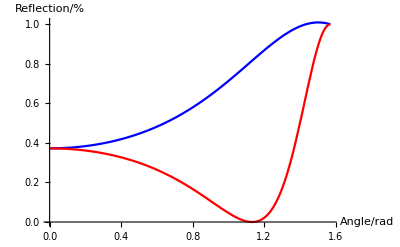

Desktop/uni_at_DIFI/materiale_corsi/laboratorio_3/project/figures/3PHmodel.pdf

```mathematica
v={d->2, λ->532};
Plot[{{Rs[θ]/.v},{Rp[θ]/.v }, Abs[β[θ]]/.v},{θ,0,π/2}, PlotStyle->{Blue,Red},AxesLabel->{"Angle/rad", "Reflection/%"}]
Export["Desktop/uni_at_DIFI/materiale_corsi/laboratorio_3/project/figures/3PHmodel.pdf",%]
```

```mathematica
r3PHp[θ]/.v
```

((1.4607 cos(θ)-√(1-0.468682 sin^2(θ)))/(√(1-0.468682 sin^2(θ))+1.4607 cos(θ))+(ⅇ^(2/133 ⅈ π √(2.13364-sin(θ))) ((4.136+0.010205 ⅈ) cos(θ)-1.4607 √(1-(0.124725-0.000615486 ⅈ) sin^2(θ))))/(1.4607 √(1-(0.124725-0.000615486 ⅈ) sin^2(θ))+(4.136+0.010205 ⅈ) cos(θ)))/(1+(ⅇ^(2/133 ⅈ π √(2.13364-sin(θ))) (1.4607 cos(θ)-√(1-0.468682 sin^2(θ))) ((4.136+0.010205 ⅈ) cos(θ)-1.4607 √(1-(0.124725-0.000615486 ⅈ) sin^2(θ))))/((√(1-0.468682 sin^2(θ))+1.4607 cos(θ)) (1.4607 √(1-(0.124725-0.000615486 ⅈ) sin^2(θ))+(4.136+0.010205 ⅈ) cos(θ))))